```mathematica
Hamil[N_,t_,μ_,Vz_,Δ_,α_]:=Module[{Temp},
Temp=Table[0,{i,1,4*N},{j,1,4*N}];

For[i=1,i<4N+1,i=i+4,Temp[[i]][[i]]=-μ];
For[i=1,i<4N+1,i=i+4,Temp[[i+1]][[i+1]]=-μ];
For[i=1,i<4N+1,i=i+4,Temp[[i+2]][[i+2]]=μ];
For[i=1,i<4N+1,i=i+4,Temp[[i+3]][[i+3]]=μ];

For[i=1,i<4N+1,i=i+4,Temp[[i]][[i+1]]=Temp[[i]][[i+1]]+Vz];
For[i=1,i<4N+1,i=i+4,Temp[[i+1]][[i]]=Temp[[i+1]][[i]]+Vz];
For[i=1,i<4N+1,i=i+4,Temp[[i+2]][[i+3]]=Temp[[i+2]][[i+3]]+Vz];
For[i=1,i<4N+1,i=i+4,Temp[[i+3]][[i+2]]=Temp[[i+3]][[i+2]]+Vz];

For[i=1,i<4N+1,i=i+4,Temp[[i]][[i+2]]=Temp[[i]][[i+2]]+Δ];
For[i=1,i<4N+1,i=i+4,Temp[[i+2]][[i]]=Temp[[i+2]][[i]]+Δ];
For[i=3,i<4N+1,i=i+4,Temp[[i-1]][[i+1]]=Temp[[i-1]][[i+1]]+Δ];
For[i=3,i<4N+1,i=i+4,Temp[[i+1]][[i-1]]=Temp[[i+1]][[i-1]]+Δ];

If[N>1,For[i=5,i<4N+1,i=i+4,Temp[[i-4]][[i]]=Temp[[i-4]][[i]]-t]];
If[N>1,For[i=5,i<4N+1,i=i+4,Temp[[i-3]][[i+1]]=Temp[[i-3]][[i+1]]-t]];
If[N>1,For[i=5,i<4N+1,i=i+4,Temp[[i-2]][[i+2]]=Temp[[i-2]][[i+2]]+t]];
If[N>1,For[i=5,i<4N+1,i=i+4,Temp[[i-1]][[i+3]]=Temp[[i-1]][[i+3]]+t]];

If[N>1,For[i=5,i<4N+1,i=i+4,Temp[[i]][[i-4]]=Temp[[i]][[i-4]]-t]];
If[N>1,For[i=5,i<4N+1,i=i+4,Temp[[i+1]][[i-3]]=Temp[[i+1]][[i-3]]-t]];
If[N>1,For[i=5,i<4N+1,i=i+4,Temp[[i+2]][[i-2]]=Temp[[i+2]][[i-2]]+t]];
If[N>1,For[i=5,i<4N+1,i=i+4,Temp[[i+3]][[i-1]]=Temp[[i+3]][[i-1]]+t]];

If[N>1,For[i=5,i<4N+1,i=i+4,Temp[[i-4]][[i+1]]=Temp[[i-4]][[i+1]]-α]];
If[N>1,For[i=5,i<4N+1,i=i+4,Temp[[i-3]][[i]]=Temp[[i-3]][[i]]+α]];
If[N>1,For[i=5,i<4N+1,i=i+4,Temp[[i-2]][[i+3]]=Temp[[i-2]][[i+3]]+α]];
If[N>1,For[i=5,i<4N+1,i=i+4,Temp[[i-1]][[i+2]]=Temp[[i-1]][[i+2]]-α]];

If[N>1,For[i=5,i<4N+1,i=i+4,Temp[[i+1]][[i-4]]=Temp[[i+1]][[i-4]]-α]];
If[N>1,For[i=5,i<4N+1,i=i+4,Temp[[i]][[i-3]]=Temp[[i]][[i-3]]+α]];
If[N>1,For[i=5,i<4N+1,i=i+4,Temp[[i+3]][[i-2]]=Temp[[i+3]][[i-2]]+α]];
If[N>1,For[i=5,i<4N+1,i=i+4,Temp[[i+2]][[i-1]]=Temp[[i+2]][[i-1]]-α]];

Temp
]
```

```mathematica
ListPlot[Eigenvalues[Hamil[100,1,2,2,1,0.6]],PlotRange->{All,{-5,5}},PlotMarkers->".1d(*
Graphics3DBox[GraphicsComplex3DBox[NCache[{{0, 0, (Rational[9, 8] + Rational[3, 8] 5^Rational[1, 2])^Rational[1, 2]}, {0, 0, Rational[-1, 2] (Rational[3, 2] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {(Rational[1, 8] + Rational[-1, 24] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 4] (-3 - 5^Rational[1, 2]), (Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2]}, {(Rational[1, 8] + Rational[-1, 24] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 4] (3 + 5^Rational[1, 2]), (Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2]}, {(Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 4] (-1 - 5^Rational[1, 2]), Rational[-1, 2] (Rational[5, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {(Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 4] (1 + 5^Rational[1, 2]), Rational[-1, 2] (Rational[5, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {(Rational[5, 8] + Rational[5, 24] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 4] (-1 - 5^Rational[1, 2]), (Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2]}, {(Rational[5, 8] + Rational[5, 24] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 4] (1 + 5^Rational[1, 2]), (Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2]}, {-(Rational[3, 4] + Rational[1, 3] 5^Rational[1, 2])^Rational[1, 2], Rational[-1, 2], (Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2]}, {-(Rational[3, 4] + Rational[1, 3] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 2], (Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2]}, {(Rational[3, 4] + Rational[1, 3] 5^Rational[1, 2])^Rational[1, 2], Rational[-1, 2], Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {(Rational[3, 4] + Rational[1, 3] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 2], Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {-(Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2], 0, Rational[-1, 2] (Rational[5, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2], Rational[1, 4] (-1 - 5^Rational[1, 2]), (Rational[5, 8] + Rational[5, 24] 5^Rational[1, 2])^Rational[1, 2]}, {Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2], Rational[1, 4] (1 + 5^Rational[1, 2]), (Rational[5, 8] + Rational[5, 24] 5^Rational[1, 2])^Rational[1, 2]}, {(Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2], 0, (Rational[5, 8] + Rational[5, 24] 5^Rational[1, 2])^Rational[1, 2]}, {Rational[-1, 2] (Rational[5, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2], Rational[1, 4] (-1 - 5^Rational[1, 2]), Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {Rational[-1, 2] (Rational[5, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2], Rational[1, 4] (1 + 5^Rational[1, 2]), Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {Root[1 - 36 #^2 + 144 #^4& , 2, 0], Rational[1, 4] (-3 - 5^Rational[1, 2]), Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {Root[1 - 36 #^2 + 144 #^4& , 2, 0], Rational[1, 4] (3 + 5^Rational[1, 2]), Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}}, {{0, 0, 1.4012585384440737`}, {0, 0, -1.4012585384440737`}, {0.17841104488654497`, -1.3090169943749475`, 0.46708617948135783`}, {0.17841104488654497`, 1.3090169943749475`, 0.46708617948135783`}, {0.46708617948135783`, -0.8090169943749475, -1.0444364486709836`}, {0.46708617948135783`, 0.8090169943749475, -1.0444364486709836`}, {1.0444364486709836`, -0.8090169943749475, 0.46708617948135783`}, {1.0444364486709836`, 0.8090169943749475, 0.46708617948135783`}, {-1.2228474935575286`, -0.5, 0.46708617948135783`}, {-1.2228474935575286`, 0.5, 0.46708617948135783`}, {1.2228474935575286`, -0.5, -0.46708617948135783`}, {1.2228474935575286`, 0.5, -0.46708617948135783`}, {-0.9341723589627157, 0, -1.0444364486709836`}, {-0.46708617948135783`, -0.8090169943749475, 1.0444364486709836`}, {-0.46708617948135783`, 0.8090169943749475, 1.0444364486709836`}, {0.9341723589627157, 0, 1.0444364486709836`}, {-1.0444364486709836`, -0.8090169943749475, -0.46708617948135783`}, {-1.0444364486709836`, 0.8090169943749475, -0.46708617948135783`}, {-0.17841104488654494`, -1.3090169943749475`, -0.46708617948135783`}, {-0.17841104488654494`, 1.3090169943749475`, -0.46708617948135783`}}], Polygon3DBox[{{15, 10, 9, 14, 1}, {2, 6, 12, 11, 5}, {5, 11, 7, 3, 19}, {11, 12, 8, 16, 7}, {12, 6, 20, 4, 8}, {6, 2, 13, 18, 20}, {2, 5, 19, 17, 13}, {4, 20, 18, 10, 15}, {18, 13, 17, 9, 10}, {17, 19, 3, 14, 9}, {3, 7, 16, 1, 14}, {16, 8, 4, 15, 1}}]],
Boxed->False,
ImageSize->30,
ViewPoint->{1.3, -2.4, 2.},
ViewVertical->{0., 0., 1.}])",Frame->True]
```

-Graphics-

```mathematica
AA=Eigenvectors[Hamil[100,1,2,2,1,0.6]]
```

```mathematica
1+1
```

2

```mathematica
Hamil[N_,t_,tp_,μ_,Δ_,ϕ_]:=Module[{Temp},
Temp=Table[0,{i,1,2*N},{j,1,2*N}];

For[i=1,i<2N+1,i=i+2,Temp[[i]][[i]]=-μ];
For[i=1,i<2N+1,i=i+2,Temp[[i+1]][[i+1]]=μ];

For[i=2,i<2N,i=i+2,Temp[[i]][[i+1]]=Temp[[i]][[i+1]]+Δ];
For[i=3,i<2N+1,i=i+2,Temp[[i]][[i-1]]=Temp[[i]][[i-1]]+Δ];

If[N>1,For[i=1,i<2N-1,i=i+2,Temp[[i]][[i+2]]=Temp[[i]][[i+2]]-t]];
If[N>1,For[i=2,i<2N,i=i+2,Temp[[i]][[i+2]]=Temp[[i]][[i+2]]-t]];

If[N>1,For[i=3,i<2N+1,i=i+2,Temp[[i]][[i-2]]=Temp[[i]][[i-2]]-t]];
If[N>1,For[i=3,i<2N+1,i=i+2,Temp[[i+1]][[i-1]]=Temp[[i+1]][[i-1]]-t]];

Temp[[1]][[2N]]=Temp[[1]][[2N]]-tp (Cos[2π ϕ]+ⅈ Sin[2π ϕ]);
Temp[[2N]][[1]]=Temp[[2N]][[1]]-tp(Cos[2π ϕ]-ⅈ Sin[2π ϕ]);
Temp
]
Hamil[3,t,tp,μ,Δ,ϕ]//MatrixForm
```

(-μ | 0 | -t | 0 | 0 | -tp (Cos[2 π ϕ]+ⅈ Sin[2 π ϕ])
0 | μ | Δ | -t | 0 | 0
-t | Δ | -μ | 0 | -t | 0
0 | -t | 0 | μ | Δ | -t
0 | 0 | -t | Δ | -μ | 0
-tp (Cos[2 π ϕ]-ⅈ Sin[2 π ϕ]) | 0 | 0 | -t | 0 | μ)

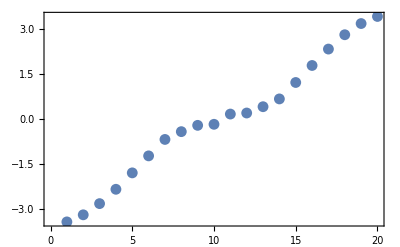

```mathematica
ListPlot[Sort[Chop[Eigenvalues[Hamil[10,1,0.2,-1.5,0.1,0.0]]]],Frame->True]
```

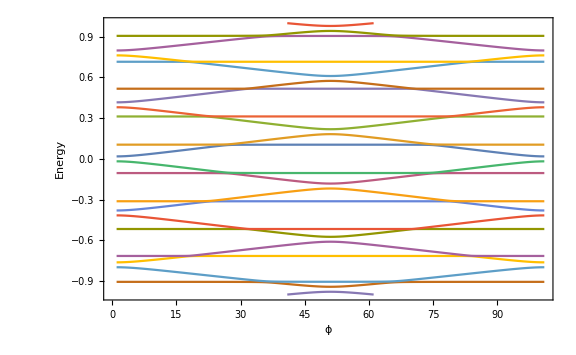

```mathematica
data=Table[Chop[Eigenvalues[Hamil[30,1,-1.5/2,0,0.1,phi]]],{phi,0,1,0.01}];
ListLinePlot[Transpose[Sort/@data],Frame->True,PlotRange->{-1,1},FrameLabel->{"ϕ","Energy"},ImageSize -> Large]
```

```mathematica
(* 5 wires *)
Hamil[N_,tpair_,timpair_,μ_,Vz_,Δ_,α_]:=Module[{Temp,Tempbis,Temp2,Temp3,Temp4,Temp5},Temp=Table[0,{i,1,4*N},{j,1,4*N}];
For[i=1,i<4 N+1,i=i+2,Temp[[i]][[i]]=Temp[[i]][[i]]+tpair-μ];
For[i=2,i<4 N+1,i=i+2,Temp[[i]][[i]]=Temp[[i]][[i]]-tpair+μ];
For[i=1,i<4 N+1,i=i+4,Temp[[i]][[i]]=Temp[[i]][[i]]+Vz];
For[i=2,i<4 N+1,i=i+4,Temp[[i]][[i]]=Temp[[i]][[i]]+Vz];
For[i=3,i<4 N+1,i=i+4,Temp[[i]][[i]]=Temp[[i]][[i]]-Vz];
For[i=4,i<4 N+1,i=i+4,Temp[[i]][[i]]=Temp[[i]][[i]]-Vz];
For[i=1,i<4 N+1,i=i+4,Temp[[i]][[i+1]]=Temp[[i]][[i+1]]-Δ];
For[i=1,i<4 N+1,i=i+4,Temp[[i+1]][[i]]=Temp[[i+1]][[i]]-Δ];
For[i=3,i<4 N+1,i=i+4,Temp[[i]][[i+1]]=Temp[[i]][[i+1]]+Δ];
For[i=3,i<4 N+1,i=i+4,Temp[[i+1]][[i]]=Temp[[i+1]][[i]]+Δ];
If[N>1,For[i=5,i<4 N+1,i=i+2,Temp[[i]][[i-4]]=Temp[[i]][[i-4]]-tpair/2]];
If[N>1,For[i=5,i<4 N+1,i=i+2,Temp[[i-4]][[i]]=Temp[[i-4]][[i]]-tpair/2]];
If[N>1,For[i=6,i<4 N+1,i=i+2,Temp[[i-4]][[i]]=Temp[[i-4]][[i]]+tpair/2]];
If[N>1,For[i=6,i<4 N+1,i=i+2,Temp[[i]][[i-4]]=Temp[[i]][[i-4]]+tpair/2]];
If[N>1,For[i=7,i<4 N+1,i=i+4,Temp[[i-6]][[i]]=Temp[[i-6]][[i]]-α/2]];
If[N>1,For[i=7,i<4 N+1,i=i+4,Temp[[i-3]][[i-1]]=Temp[[i-3]][[i-1]]+α/2]];
If[N>1,For[i=8,i<4 N+1,i=i+4,Temp[[i-6]][[i]]=Temp[[i-6]][[i]]-α/2]];
If[N>1,For[i=5,i<4 N+1,i=i+4,Temp[[i-2]][[i]]=Temp[[i-2]][[i]]+α/2]];
If[N>1,For[i=7,i<4 N+1,i=i+4,Temp[[i]][[i-6]]=Temp[[i]][[i-6]]-α/2]];
If[N>1,For[i=8,i<4 N+1,i=i+4,Temp[[i]][[i-6]]=Temp[[i]][[i-6]]-α/2]];
If[N>1,For[i=5,i<4 N+1,i=i+4,Temp[[i]][[i-2]]=Temp[[i]][[i-2]]+α/2]];
If[N>1,For[i=6,i<4 N+1,i=i+4,Temp[[i]][[i-2]]=Temp[[i]][[i-2]]+α/2]];
Tempbis=Table[0,{i,1,4*N},{j,1,4*N}];
For[i=1,i<4 N+1,i=i+2,Tempbis[[i]][[i]]=Tempbis[[i]][[i]]-timpair/2];
For[i=2,i<4 N+1,i=i+2,Tempbis[[i]][[i]]=Tempbis[[i]][[i]]+timpair/2];
Temp2=Transpose[Join[Transpose[Temp],Transpose[Tempbis],Table[0,{i,1,4*N},{j,1,4*N}]]];
Temp3=Transpose[Join[Transpose[Tempbis],Transpose[Temp],Transpose[Tempbis]]];
Temp4=Transpose[Join[Table[0,{i,1,4*N},{j,1,4*N}],Transpose[Tempbis],Transpose[Temp]]];
Temp5=Join[Temp2,Temp3,Temp4];
Temp5]
```

```mathematica
(*Hamil[N_,tpair_,timpair_,μ_,Vz_,Δ_,α_]*)
ListPlot[Eigenvalues[Hamil[50,1,0,2,2,1,0.6]],PlotRange->{All,{-5,5}},PlotMarkers->".1d(*
Graphics3DBox[GraphicsComplex3DBox[NCache[{{0, 0, (Rational[9, 8] + Rational[3, 8] 5^Rational[1, 2])^Rational[1, 2]}, {0, 0, Rational[-1, 2] (Rational[3, 2] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {(Rational[1, 8] + Rational[-1, 24] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 4] (-3 - 5^Rational[1, 2]), (Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2]}, {(Rational[1, 8] + Rational[-1, 24] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 4] (3 + 5^Rational[1, 2]), (Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2]}, {(Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 4] (-1 - 5^Rational[1, 2]), Rational[-1, 2] (Rational[5, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {(Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 4] (1 + 5^Rational[1, 2]), Rational[-1, 2] (Rational[5, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {(Rational[5, 8] + Rational[5, 24] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 4] (-1 - 5^Rational[1, 2]), (Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2]}, {(Rational[5, 8] + Rational[5, 24] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 4] (1 + 5^Rational[1, 2]), (Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2]}, {-(Rational[3, 4] + Rational[1, 3] 5^Rational[1, 2])^Rational[1, 2], Rational[-1, 2], (Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2]}, {-(Rational[3, 4] + Rational[1, 3] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 2], (Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2]}, {(Rational[3, 4] + Rational[1, 3] 5^Rational[1, 2])^Rational[1, 2], Rational[-1, 2], Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {(Rational[3, 4] + Rational[1, 3] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 2], Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {-(Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2], 0, Rational[-1, 2] (Rational[5, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2], Rational[1, 4] (-1 - 5^Rational[1, 2]), (Rational[5, 8] + Rational[5, 24] 5^Rational[1, 2])^Rational[1, 2]}, {Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2], Rational[1, 4] (1 + 5^Rational[1, 2]), (Rational[5, 8] + Rational[5, 24] 5^Rational[1, 2])^Rational[1, 2]}, {(Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2], 0, (Rational[5, 8] + Rational[5, 24] 5^Rational[1, 2])^Rational[1, 2]}, {Rational[-1, 2] (Rational[5, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2], Rational[1, 4] (-1 - 5^Rational[1, 2]), Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {Rational[-1, 2] (Rational[5, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2], Rational[1, 4] (1 + 5^Rational[1, 2]), Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {Root[1 - 36 #^2 + 144 #^4& , 2, 0], Rational[1, 4] (-3 - 5^Rational[1, 2]), Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {Root[1 - 36 #^2 + 144 #^4& , 2, 0], Rational[1, 4] (3 + 5^Rational[1, 2]), Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}}, {{0, 0, 1.4012585384440737`}, {0, 0, -1.4012585384440737`}, {0.17841104488654497`, -1.3090169943749475`, 0.46708617948135783`}, {0.17841104488654497`, 1.3090169943749475`, 0.46708617948135783`}, {0.46708617948135783`, -0.8090169943749475, -1.0444364486709836`}, {0.46708617948135783`, 0.8090169943749475, -1.0444364486709836`}, {1.0444364486709836`, -0.8090169943749475, 0.46708617948135783`}, {1.0444364486709836`, 0.8090169943749475, 0.46708617948135783`}, {-1.2228474935575286`, -0.5, 0.46708617948135783`}, {-1.2228474935575286`, 0.5, 0.46708617948135783`}, {1.2228474935575286`, -0.5, -0.46708617948135783`}, {1.2228474935575286`, 0.5, -0.46708617948135783`}, {-0.9341723589627157, 0, -1.0444364486709836`}, {-0.46708617948135783`, -0.8090169943749475, 1.0444364486709836`}, {-0.46708617948135783`, 0.8090169943749475, 1.0444364486709836`}, {0.9341723589627157, 0, 1.0444364486709836`}, {-1.0444364486709836`, -0.8090169943749475, -0.46708617948135783`}, {-1.0444364486709836`, 0.8090169943749475, -0.46708617948135783`}, {-0.17841104488654494`, -1.3090169943749475`, -0.46708617948135783`}, {-0.17841104488654494`, 1.3090169943749475`, -0.46708617948135783`}}], Polygon3DBox[{{15, 10, 9, 14, 1}, {2, 6, 12, 11, 5}, {5, 11, 7, 3, 19}, {11, 12, 8, 16, 7}, {12, 6, 20, 4, 8}, {6, 2, 13, 18, 20}, {2, 5, 19, 17, 13}, {4, 20, 18, 10, 15}, {18, 13, 17, 9, 10}, {17, 19, 3, 14, 9}, {3, 7, 16, 1, 14}, {16, 8, 4, 15, 1}}]],
Boxed->False,
ImageSize->30,
ViewPoint->{1.3, -2.4, 2.},
ViewVertical->{0., 0., 1.}])",Frame->True]
```

-Graphics-